### Categorization

Tutorial

Fusica

Fusica`

Fusica/tutorial/Introduction to Fusica

### Keywords

$Tracker

⋄

CopyTo

Core Language

Definition

Diamond

Fuse

FusePattern

Fusica

Inheritance

Object-oriented Programming

Symbol

Details

Tom Dela Haije

# Introduction to Fusica

### Overview

The Fusica package introduces a number of new symbols in the "Fusica`" context.

$Tracker | Enables or disables automatic updating of symbols create by Fuse 
CopyTo | Copies definitions from one symbol to another
Fuse | Creates a new symbol that combines values, definitions, options, and attributes of a set of symbols
FusePattern | Represents a pattern object that matches symbols created by Fuse

Fusica symbols.

Before the Fusica package can be used, it needs to be loaded using Get or Needs.

Load the Fusica package:

```mathematica
Needs["Fusica`"]
```

### Background and Terminology

Consider the behavior of a symbol d with as its ownvalue — assigned using Set or SetDelayed — another symbol a.

Define a function a and assign it as an ownvalue to d:

```mathematica
a[x_]:=x^2
d=a;
```

The symbol d will be referred to as an "alias" of a, and can be considered to be equal to a for most purposes. It evaluates to the same values, and additional definitions for a are immediately used by d.

d produces the same values as a, and when a is changed d immediately uses the new definitions:

```mathematica
d/@Range[3]
```

{1,4,9}

```mathematica
a[2]=1;
```

```mathematica
d/@Range[3]
```

{1,1,9}

Downvalues created for d result in new downvalues for a instead of d, but ownvalues created for d overwrite the existing ownvalues of d instead of a:

```mathematica
d[3]=1;
```

```mathematica
d/@Range[3]
```

{1,1,1}

```mathematica
Definition[a]
```

a[2]=1
 
a[3]=1
 
a[x_]:=x^2

```mathematica
d=1;
```

```mathematica
Definition[d]
```

d=1

The aim of the Fusica package is to generalize this behavior, allowing multiple symbols on the right hand side of a definition:

The Fusica package implements functionality to support definitions of the form:

```mathematica
s=b⋄c;
```

In this tutorial, the symbol that is assigned to will be referred to as the "fused symbol", whereas the symbols on the right hand side whose definitions are combined into the fused symbol will be referred to as the "source symbols".

### Combining Definitions with Fuse

Fused symbols can be created with the function Fuse. Fuse combines the definitions associated to one or several source symbols and uses them when creating a new "shadow" symbol. These shadow symbols reside in the "Fusica`Shadows`" context and are by default formatted as grayed out symbols connected with ⋄ (Diamond). By definition, fused symbols are aliases of shadow symbols.

Define functions f and g:

```mathematica
f[x_Integer]:=x
f[4]:=0
g[x_]:=x^2
```

Create a fused symbol fg combining the definitions of the source symbols f and g:

```mathematica
fg=Fuse[f,g]
```

f⋄g

```mathematica
Definition[fg]
```

fg=f⋄g

```mathematica
FullForm[fg]
```

Fusica`Shadows`$11

Fused symbols can be used almost exactly analogous to normal symbols or aliases:

```mathematica
fg/@Range[1,5,1/2]
```

{1,9/4,2,25/4,3,49/4,0,81/4,5}

Fuse flattens out shadow symbols and removes repeated symbols, so that shadow symbols — and, effectively, fused symbols — can be combined with others.

Fused symbols can themselves be fused:

```mathematica
h[5]:=2;
```

```mathematica
fgh=Fuse[fg,h]
```

f⋄g⋄h

```mathematica
fgh/@Range[1,5,1/2]
```

{1,9/4,2,25/4,3,49/4,0,81/4,2}

Definitions of repeated symbols will never be used, and are hence removed before the creation of a shadow symbol. The order of the source symbols always remains unchanged:

```mathematica
Fuse[h,fg,g,f,g,h]
```

h⋄f⋄g

Unless Diamond is protected when the Fusica package is loaded, or if it already has a value, this symbol and its alternative input forms can also be used to specify fused symbols.

Diamond (⋄) can be used to define fused symbols:

```mathematica
(f⋄g)==Fuse[f,g]==fg
```

True

### Modified Definitions

Shadow symbols are updated at evaluation, so changes to the definitions of the combined source symbols are incorporated almost immediately into the fused symbol.

When the source symbol f is modified, the new definition is immediately used by the fused symbol fg:

```mathematica
f[1]=3;
```

```mathematica
fg[1]
```

3

Functions that hold a symbol in an unevaluated form will prevent the automatic updating from taking place, and may produce results based on outdated cached definitions. Since shadow symbols are typically referenced by an alias this should not be a common occurrence.

Functions that have attributes such as HoldFirst or HoldAll may prevent automatic definition updates of a shadow symbol from taking place, producing outdated results:

```mathematica
ClearAttributes[Evaluate@fg,ReadProtected]
```

```mathematica
f[20,15]=13;
```

```mathematica
DownValues[Fusica`Shadows`$11]//Column
```

HoldPattern[(f⋄g)[1]]:>3
HoldPattern[(f⋄g)[4]]:>0
HoldPattern[(f⋄g)[x_Integer]]:>x
HoldPattern[(f⋄g)[x_]]:>x^2

```mathematica
DownValues[Evaluate@fg]//Column
```

HoldPattern[(f⋄g)[1]]:>3
HoldPattern[(f⋄g)[4]]:>0
HoldPattern[(f⋄g)[20,15]]:>13
HoldPattern[(f⋄g)[x_Integer]]:>x
HoldPattern[(f⋄g)[x_]]:>x^2

Although fused symbols can be used like regular symbols in many regards, it is important to remember that they are aliases, and hence that they are replaced by their shadow symbol before any other definitions can be tried. As such there is little point in defining for example downvalues for a fused symbol.

A fused symbol with downvalues will only evaluate the definitions of the shadow symbol:

```mathematica
fusedWithDown[x_]:=x+1
fusedWithDown=Fuse[h];
```

```mathematica
Definition[fusedWithDown]
```

fusedWithDown=h
 
fusedWithDown[x_]:=x+1

```mathematica
fusedWithDown/@Range[5]
```

{h[1],h[2],h[3],h[4],2}

While the usual alias definition directly links an alias with a single source symbol — allowing for example value definitions to be applied to the source symbol (recall Background and Terminology) — shadow symbols do not have a unique source symbol. This being the case, shadow symbols cannot apply new value definitions unambiguously, and consequently this functionality is lost. New definitions intended for fused symbols should hence be explicitly created for the source symbols. Attempts to assign to a fused symbol typically result in assignments to the shadow symbol, which has the attribute Protected to prevent these accidental assignments. (The shadow symbol should be considered reserved for internal use, and not be assigned to directly. Its Protected attribute is reset every time the symbol updates its definitions.)

Fused symbols are virtually always, even inside SetDelayed, replaced by their shadow, which is protected to prevent accidental assignments:

```mathematica
fg[1]:=10;
```

SetDelayed::write: Tag f⋄g in (f⋄g)[1] is Protected.

Fused symbols need not have attributes themselves, but the shadow symbols they evaluate to are protected by default:

```mathematica
Attributes[fg]
```

{}

```mathematica
Attributes[Evaluate@fg]
```

{Protected,ReadProtected,Temporary}

### Values and the Order of Definitions

All definitions recognized by Language`ExtendedDefinition, including OwnValues, DownValues, UpValues,  Options, and formatting rules, can be copied, and they are applied in the usual order (see also the Evaluation tech note). The default behavior of Fusica is to copy all values except for ownvalues. With Fuse[f, g], the evaluator will try (ownvalues of f before ownvalues of g before) downvalues of f before downvalues of g, etc. The standard ordering based on pattern specificity described in the Transformation Rules and Definitions tutorial still applies.

When applying the values of fg, the more specific definition for g[2] is tried before the general definition for f[_Integer], even though f comes before g in fg=Fuse[f,g]:

```mathematica
g[2]=3;
```

```mathematica
Definition[f]
```

f[1]=3
 
f[4]:=0
 
f[20,15]=13
 
f[x_Integer]:=x

```mathematica
Definition[g]
```

g[2]=3
 
g[x_]:=x^2

```mathematica
fg/@Range[1,3]
```

{3,3,3}

NOTE: The default behavior of Fuse to copy all values except OwnValues makes Fuse significantly more convenient to use in many applications, while applications where it is important to include ownvalues are uncommon. For those rare situations where the fusing of ownvalues is desired, the package can be modified.

Attributes are copied as well, with the exception of the attributes Protected, Locked, Stub, and Temporary. Note that definitions that crucially depend on certain sets of attributes may not be duplicated properly if symbols have different attributes, and a warning message is generated if there is a mismatch outside of the five non-functional attributes (the four excluded attributes and ReadProtected).

Fusing symbols with mismatching attributes always triggers a warning:

```mathematica
Attributes[symbolWithAttr]=HoldAll;
```

```mathematica
fusedWithAttr=Fuse[f,symbolWithAttr]
```

Fuse::attrmm: Warning: attributes mismatch between symbols f, symbolWithAttr.

f⋄symbolWithAttr

The fused symbol still has the attributes of all source symbols (in addition to the default Protected, ReadProtected, and Temporary attributes):

```mathematica
Attributes[Evaluate@fusedWithAttr]
```

{HoldAll,Protected,ReadProtected,Temporary}

Symbols that have both ReadProtected and Locked attributes cannot be copied and will be silently ignored by Fuse. The same goes for kernel functions. Because formatting rules are copied as well, the default format for fused expressions based on Diamond will be overwritten if one of the source symbols specifies formatting rules.

Formatting definitions of source symbols will overwrite the default formatting rules for fused symbols:

```mathematica
Format[symbolWithAttr]="Looks like I have attributes!";
```

```mathematica
fusedWithAttr
```

Fuse::attrmm: Warning: attributes mismatch between symbols f, symbolWithAttr.

Looks like I have attributes!

### Fuse and Pattern Matching

Fuse reinterprets all of the source symbols that occur in the pattern on the left hand side of a definition, but not those that occur on the right hand side.

Only symbols on the left hand side of a definition are reinterpreted by Fuse. Fuse uses the original definitions for symbols on the right hand side of a self-referencing definition, such as recursive functions, mimicking the behavior observed with the usual aliasing:

```mathematica
recursiveFunction[n_Integer?Positive]:=recursiveFunction[n-1]
```

```mathematica
recursiveAlias=recursiveFunction;
recursiveAlias[3]
```

recursiveFunction[0]

```mathematica
DownValues[h]//Column
```

HoldPattern[h[5]]:>2

```mathematica
Fuse[h,recursiveFunction][10]
```

recursiveFunction[0]

When reinterpretation is also desired in the right hand side, we may use the following basic pattern.

In custom functions a simple pattern can be used to ensure reinterpretation of source symbols on the right hand side of a definition:

```mathematica
(head:recursiveFusible)[n_Integer?Positive]:=head[n-1]
```

```mathematica
Fuse[h,recursiveFusible][10]
```

2

Any patterns wrapped in Verbatim are excluded from Fuse-related replacements, allowing more precise control on the arguments for which functions are defined.

Patterns wrapped in Verbatim on the left hand side of a definition are not reinterpreted by Fuse, and only source symbols occurring outside those patterns will refer to the fused symbol:

```mathematica
p[p]:=1;
q[Verbatim[q]]:=1;
```

```mathematica
DownValues[Evaluate[Fuse[p]]]//Column
```

HoldPattern[p[p]]:>1

```mathematica
DownValues[Evaluate[Fuse[q]]]//Column
```

HoldPattern[q[Verbatim[q]]]:>1

In the following example, Fuse[p] is only defined for Fuse[p], because both occurrences of p in the original definition are reinterpreted by Fuse. Fuse[q] only has a value for the original source symbol q:

```mathematica
Fuse[p][p]
Fuse[p][Fuse[p]]
```

p[p]

1

```mathematica
Fuse[q][q]
Fuse[q][Fuse[q]]
```

1

q[q]

Unlike alias symbols, fused symbols are not treated as identical to their source symbols for pattern matching purposes — not even if there is only one source symbol.

Fused symbols are not matched with their source symbols by pattern matching functions:

```mathematica
MatchQ[recursiveAlias,recursiveFunction]
```

True

```mathematica
MatchQ[Fuse[h],h]
```

False

Consequently, functions defined for a source symbol do not automatically work with fused symbols.

Functions defined for a source symbol do not automatically recognize fused symbols in their arguments:

```mathematica
function[x_f]:={Head[x],Hold@@x}
```

```mathematica
function[f[1,2,3]]
```

{f,Hold[1,2,3]}

```mathematica
function[fg[1,2,3]]
```

function[(f⋄g)[1,2,3]]

FusePattern makes it easier to define source symbol values that apply to the source symbol as well as any fused symbols.

FusePattern can be used to create patterns that match a specific symbol, as well as any shadow symbols that have this symbol as a source symbol:

```mathematica
functionForFuse[x:(f|FusePattern[f,___])[___]]:={Head[x],Hold@@x}
```

```mathematica
functionForFuse[f[1,2,3]]
```

{f,Hold[1,2,3]}

```mathematica
functionForFuse[fg[1,2,3]]
```

{f⋄g,Hold[1,2,3]}

### Set versus SetDelayed

As in the standard aliasing case that inspired Fuse, there are some noteworthy subtleties in the distinctions between fused symbols defined using Set and SetDelayed.

Fused symbols created with Set fuse together the definitions of the (evaluated) source symbols at the time that Fuse is evaluated. If a symbol evaluates to a shadow symbol when the fused symbol is created then the definitions of that shadow symbol is used by Fuse. If, on the other hand, a symbol is given a shadow ownvalue after Fuse was evaluated, the fused symbol will still use the definition of the original source symbol and disregard the definitions associated to the new shadow symbol.

Fuse normally evaluates its arguments and flattens out any shadow symbols:

```mathematica
Fuse[f,Fuse[g,h]]==fgh==Fuse[f,g,h]
```

True

If a source symbol is given a shadow ownvalue after the creation of a fused symbol, a fused symbol created with Set will still use the definitions of the original source symbol only:

```mathematica
k[5]=8;
h=Fuse[k];
```

```mathematica
Definition[h]
```

h=k
 
h[5]:=2

```mathematica
h[5]
```

8

```mathematica
fgh[5]
```

2

Fused symbols created with SetDelayed behave more intuitively in this regard, as they re-evaluate their source symbols whenever the fused symbol is evaluated.

SetDelayed can be used to create fused symbols that re-evaluate their source symbols at evaluation:

```mathematica
fgh:=Fuse[f,g,h];
h:=Fuse[k];
```

```mathematica
k[5]=10;
fgh[5]
```

10

Fused symbols created with SetDelayed do have the downside that they can lead to infinite recursions, so care must be taken in this case to prevent cyclical definitions.

SetDelayed can lead to infinite recursions:

```mathematica
k:=Fuse[fgh];
fgh
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Fuse[fgh].

Fuse[f,g,h]

```mathematica
h=.;
```

In most common scenarios it is natural to set Fuse definitions for symbols before they are fused with others, and in these cases Set will remove some of the Unevaluated clutter that is necessary in the case of SetDelayed. However, as always with Set and SetDelayed it is usually better to opt for SetDelayed when in doubt.

### Self-fused Symbols

Symbols can self-fuse, essentially allowing for (multiple) inheritance.

Symbols can be fused with themselves using this basic pattern:

```mathematica
f:=Fuse[Unevaluated[f],g]
g:=Fuse[Unevaluated[g],h]
```

```mathematica
ClearAttributes[Evaluate@f,ReadProtected]
```

```mathematica
DownValues[Evaluate@f]//Column
```

HoldPattern[(f⋄g⋄h)[1]]:>3
HoldPattern[(f⋄g⋄h)[2]]:>3
HoldPattern[(f⋄g⋄h)[4]]:>0
HoldPattern[(f⋄g⋄h)[5]]:>2
HoldPattern[(f⋄g⋄h)[20,15]]:>13
HoldPattern[(f⋄g⋄h)[x_Integer]]:>x
HoldPattern[(f⋄g⋄h)[x_]]:>x^2

```mathematica
f/@Range[1,4,1/2]
```

{3,9/4,3,25/4,3,49/4,0}

```mathematica
g/@Range[1,4,1/2]
```

{1,9/4,3,25/4,9,49/4,16}

The Unevaluated on the right hand side prevents f from re-evaluating to its shadow after the definition, which prevents an infinite recursion.

Self-fused definitions based on SetDelayed require the use of Unevaluated or related constructs to prevent infinite recursions:

```mathematica
selfFusedWithoutUnevaluated:=Fuse[selfFusedWithoutUnevaluated];
```

```mathematica
selfFusedWithoutUnevaluated
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Fuse[selfFusedWithoutUnevaluated].

Fuse[selfFusedWithoutUnevaluated]

Had we used Set instead of SetDelayed, the Unevaluated wrapper could have been omitted in the definitions of the self-fused symbols. However, we would then have to work around the disadvantages that come with the usage of Set, as described in the previous section.

There is still one caveat to consider though, and that is that self-fused symbols cannot be modified in the standard way; as fused symbols they immediately evaluate to their protected shadows. It was suggested before that new definitions be added to the source symbols directly, but this of course no longer applies in the case of self-fused symbols.

Self-fused symbols evaluate to their shadows inside Set and SetDelayed, preventing the addition of new definitions in the standard way:

```mathematica
f[3]=π;
```

Set::write: Tag f⋄g⋄h in (f⋄g⋄h)[3] is Protected.

```mathematica
f[3]
```

3

There are two recommended solutions to simplify the addition of new definitions to self-fused symbols. The first one is to make use of HoldPattern. This straightforwardly prevents the self-fused symbol on the left hand side of a definition from evaluating to its shadow.

HoldPattern can be used to prevent a self-fused symbol from evaluating to its shadow, allowing the addition of new definitions:

```mathematica
HoldPattern[f][3]=π;
```

```mathematica
f[3]
```

π

Alternatively, one can use a toggle variable in the definition of the self-fused symbol, which allows the definition to be disabled locally.

A toggle variable can be used to locally disable the delayed definition of a fused symbol, permitting the addition of new definitions:

```mathematica
$i=True;i:=Fuse[Unevaluated[i],f]/;$i;
```

```mathematica
i[1]=√2;
```

Set::write: Tag i⋄f⋄g⋄h in (i⋄f⋄g⋄h)[1] is Protected.

```mathematica
Block[{$i},i[1]=√2];
```

```mathematica
i/@Range[1,5,1/2]
```

{√2,9/4,3,25/4,π,49/4,0,81/4,2}

If the toggle variable is blocked in the original definition of the fused symbol then the Unevaluated on the right hand side may be omitted:

```mathematica
i:=Block[{$i},Fuse[i,f]]/;$i;
```

```mathematica
i/@Range[1,5,1/2]
```

{√2,9/4,3,25/4,π,49/4,0,81/4,2}

### Fusica Overhead

The overhead added by checking for changes in symbols is relatively significant — typically several orders of magnitude difference.

While the evaluation of non-fused symbols is very inexpensive, there is a check for modifications to the source symbols of a fused symbol that takes some time:

```mathematica
Do[d,{10000}];//RepeatedTiming//First
```

0.00026

```mathematica
Do[f,{10000}];//RepeatedTiming//First
```

0.63

However, the overhead is added to a low-cost, low-frequency operation, so the cost is generally not be too problematic in practice. One convenient way to reduce this overhead in cases where efficiency is essential and where definitions are known to be constant, is to temporarily force the use of cached definitions by blocking the toggle variable $Tracker. (Regardless of the value of $Tracker, shadow definition updates can be triggered manually using Update, see also the examples in the documentation for $Tracker.)

Blocking $Tracker blocks the self-updating definitions of shadow symbols, which forces the use of cached definitions and significantly reduces the Fuse-related overhead:

```mathematica
Block[{$Tracker},With[{f=f},Do[f,{10000}]//RepeatedTiming//First]
]
```

0.001

The overhead can be removed completely by creating a copy of the fused symbol that does not update at all, for example using CopyTo.

CopyTo can be used to create a copy of a fused symbol that does not update, completely removing the Fuse-related overhead:

```mathematica
CopyTo[f];
```

```mathematica
Do[f,{10000}];//RepeatedTiming//First
```

0.0000939

```mathematica
f/@Range[1,5,1/2]
```

{1,9/4,3,25/4,9,49/4,16,81/4,2}

CopyTo uses the same mechanisms as Fuse to copy definitions from one symbol to another.

CopyTo can create copies of symbols using the same mechanisms as Fuse:

```mathematica
CopyTo[myPlot,Plot]
```

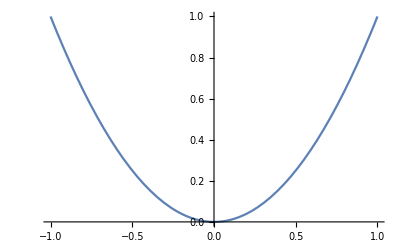

```mathematica
myPlot[x^2,{x,-1,1}]
```

More About

Related Tutorials

Related Wolfram Education Group Courses